## 1. 
A. How many points whose x coordinate is -6 can we plug into the function f(x,y)=3 x^2 y+2x y^3 to get an answer of 10? Explain.
B. Why is it that no points in the output of levelset[3 x^2 y+2x y^3,10] are in the fourth quadrant?

```mathematica
levelset[e_,k_]:=Module[{k1,set1},k1=k;
set1=ContourPlot[e==k1,{x,-8,8},{y,-8,8},Axes->True];
Return[set1]]
```

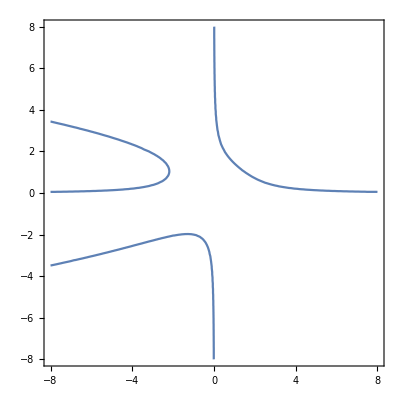

```mathematica
levelset[3 x^2 y+2x y^3,10]
```

There are 3 points whose x cordinate is -6 that we can plug into the function f(x,y)=3 x^2 y+2x y^3 to get an answer of 10. When you insert the value of -6 into the function for x and set the function equal to 10 you get 108y-12y^3=10. Since this equation is a cubic there are 3 possible solutions. 

In order to explain why no points in the output of levelset[3 x^2 y+2x y^3,10] are in the fourth quadrant we first have to look at the characteristic behavior of it’s componant parts 3x^2 and 2xy^3. Let’s start by graphing them.

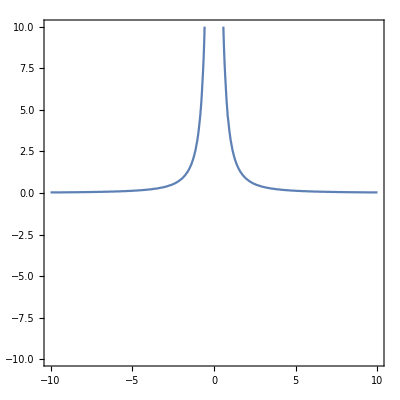

```mathematica
ContourPlot[3*x^2*y==10,{x,-10,10},{y,-10,10},Axes->True]
```

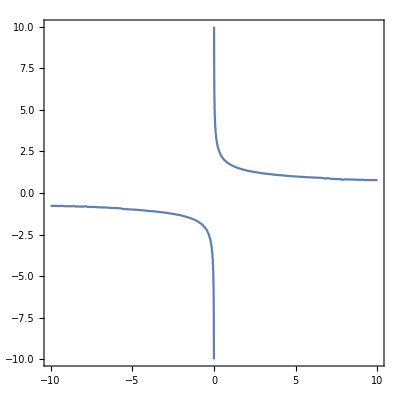

```mathematica
ContourPlot[2*x*y^3==10,{x,-10,10},{y,-10,10},Axes->True]
```

For each of these plots the value of 10 does not matter as much as the fact that 10 is a positive number. Any positive number could be substituted in it’s place to prove the same point. For 3*x^2*y=10 the graph exists in the 1st&2nd quadrants where the x and y values are [+ +] and [- +] respectivly. In the graph for 2*x*y^3  the plot exists in the 1st&3rd quadrants where the x and y values are [+ +] and [- -] respectivly. Since in the function these two terms are added the same can be assumed of their graphs to form the graph of the function. If you add the componant of the 3*x^2*y graph in the 1st quad to the componant of the 2*x*y^3 graph in the 1st quad the only outcome possible is another graph in the first quadrant with [+ +] x and y values. If you add the componant of the 3*x^2*y graph in the 1st quad to the componant of the 2*x*y^3 graph in the 3rd quad the only outcomes possible are another graph in the first quadrant with [+ +] x and y values or a graph in the 3rd quadrant with [- -] x&y values.  If you add the componant of the 3*x^2*y graph in the 2nd quad to the componant of the 2*x*y^3 graph in the 1st quad the only outcomes possible are another graph in the first quadrant with [+ +] x and y values or a graph in the 2nd quadrant with [- +] x&y values.   If you add the componant of the 3*x^2*y graph in the 2nd quad to the componant of the 2*x*y^3 graph in the 3rd quad the only outcomes possible are a graph in the 3rd quadrant with [- -] x and y values or a graph in the 2nd quadrant with [- +] x&y values.  This covers all of the possible combinations of componants of the componant parts of the function, none of which result in a possible [+ -] valued graph of x and y existing in the 4th quadrant.

## 2. Look at the level sets for f(x,y)=x^2 y^2 for a specific positive number k. The level set should have 5 different regions. Is it the case that if one component of the level set separates two points, then plugging one in point in gives a number greater than the level and plugging in the other gives a number less than the level? Pick some points to test this. Use a picture to show the relationship of the points you picked to the level set.

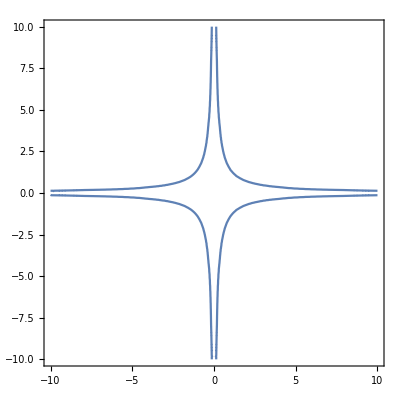

```mathematica
ContourPlot[x^2*y^2==2,{x,-10,10},{y,-10,10},Axes->True]
```

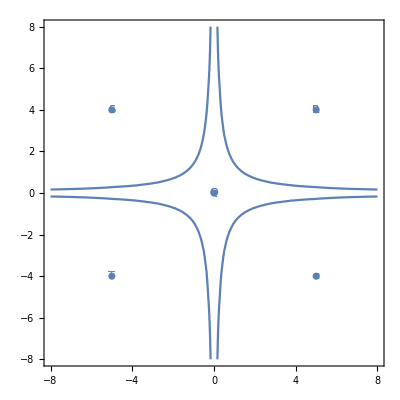

```mathematica
Show[levelset[x^2*y^2,2],ListPlot[{{0,0},{5,4},{-5,4},{-5,-4},{5,-4}}],ListPlot[{{0,0}},PlotMarkers->{"Q"}],ListPlot[{{5,4}},PlotMarkers->{"R"}],ListPlot[{{-5,4}},PlotMarkers->{"S"}],ListPlot[{{-5,-4}},PlotMarkers->{"T"}],
ListPlot[{{5,-4}},PlotMarkers->{"u"}]]
```

```mathematica
f[x_,y_]:=x^2*y^2;
f[0,0]
f[5,4]
f[-5,4]
f[-5,-4]
f[5,-4]
```

0

400

400

400

«1 more identical outputs»

It is the case that if 1(emphasis on 1) componant of the level set seperates 2 points , then plugging in 1 point gives a # >than the level and plugging in the other gives a #<than the level.

## 3. For the following, use the Show command to draw a picture combining two ContourPlots as above so that:
	1. the constraint curve  C is red; 
	2. there are enough level sets so that you can approximate the extreme values of f to within 1.
	3. What is your approximation of the maximum and minimum values?
	4. If you suspect there is either no maximum or no minimum, explain your reasoning.
	
A. 	f(x,y)=20x+30y;                    	C: x^2+y^2=4
B. 	f(x,y)=x^2 y^3                               	C: x^2+2 y^2=6
C. 	f(x,y)=(10x+100)/y                           	C:x^2+(y-8)^2=1
D.  	f(x,y)=x^2-2x+y^2+6y 		C: y=2x+1
E. 	f(x,y)=x^3-x-2y 	 		C: -6 x^2+3 y^2=6
F. 	f(x, y) = 4 x^2 - 9 y^2  			C: (x+2)^2-2y=11
For part F, to see what you’re up against, look at the following:
Show[ContourPlot[4 x^2-9 y^2,{x,-10,10},{y,-10,10},PlotRange->{-500,500},Contours→30,ContourLabels→All],ContourPlot[(x+2)^2-2 y==11,{x,-10,10},{y,-10,10},ContourStyle→Red]]

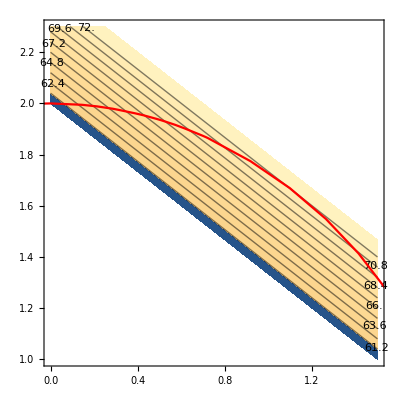

```mathematica
Show[ContourPlot[20x+30y,{x,0,1.5},{y,1,2.3},PlotRange->{60,74},Contours->10,ContourLabels->All],ContourPlot[x^2+ y^2==4,{x,-8,8},{y,-8,8},ContourStyle->Red]]
```

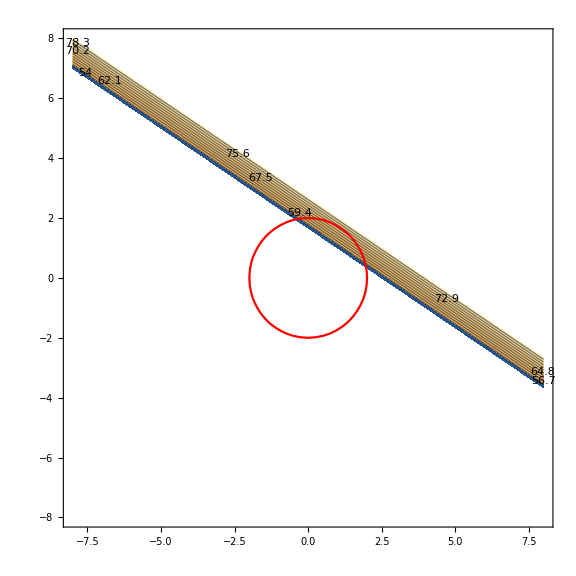

```mathematica
Show[%29,ImageSize->Large]
```

For A. the Maximum is 71 because level sets corresponding to lower levels  intersect the constraint curve. This picture suggests that no other contour will be tangent to the constraint curve therefore there will be no minimal output.

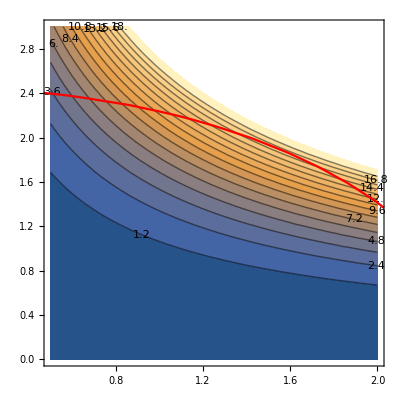

```mathematica
Show[ContourPlot[x^2*y^3,{x,0.5,2},{y,0,3},PlotRange->{0,20},Contours->15,ContourLabels->All],ContourPlot[x^2+ y^2==6,{x,-8,8},{y,-8,8},ContourStyle->Red]]
```

```mathematica
|
```

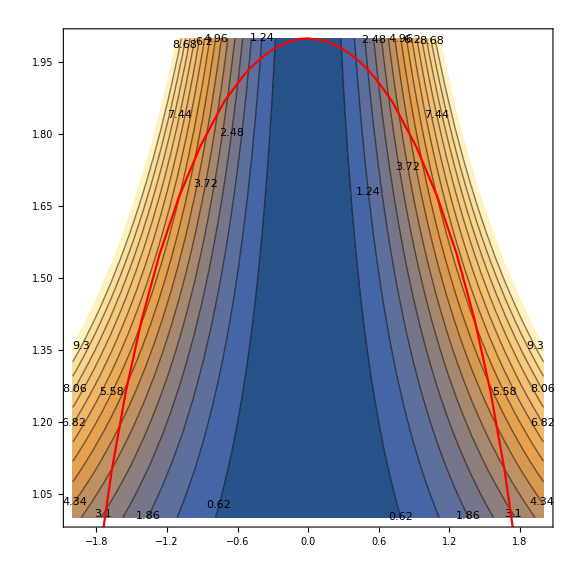

```mathematica
Show[%43,ImageSize->Large]
```

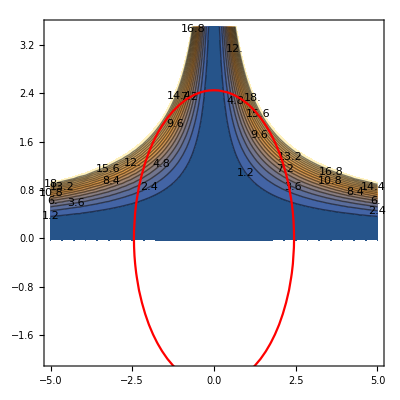

```mathematica
Show[ContourPlot[x^2*y^3,{x,-5,5},{y,-2,3.5},PlotRange->{0,20},Contours->15,ContourLabels->All],ContourPlot[x^2+ y^2==6,{x,-8,8},{y,-8,8},ContourStyle->Red]]
```

For B. The maxima is approximatly 16.2, it is a maxima because the level sets corresponding to lower levels meet the constraint curve. This picture suggests that no other contour will be tangent to the constraint curve therefore there will be no minimal output.

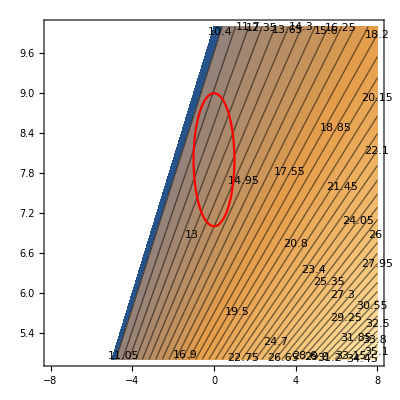

```mathematica
Show[ContourPlot[(10x+100)/y,{x,-8,8},{y,5,10},PlotRange->{10,50},Contours->60,ContourLabels->All],ContourPlot[x^2+(y-8)^2==1,{x,-4,8},{y,7,10},ContourStyle->Red]]
```

For C. 14.5 is the maximum and 11.1 is the minimum

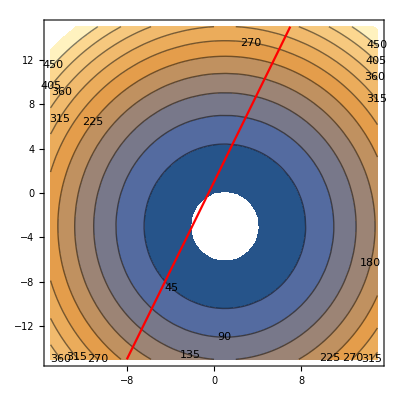

```mathematica
Show[ContourPlot[x^2-2x+y^2+6y,{x,-15,15},{y,-15,15},PlotRange->{0,500},Contours->10,ContourLabels->All],ContourPlot[y==2x+1,{x,-15,15},{y,-15,15},ContourStyle->Red]]
```

For D.There are no maxima or minima because no level set of f(x,y) is tangent to C.

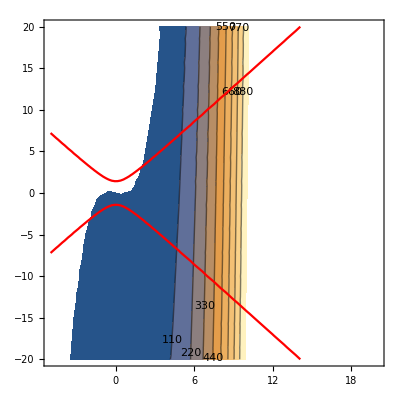

```mathematica
Show[ContourPlot[x^3-x-2y,{x,-5,20},{y,-20,20},PlotRange->{0,1000},Contours->8,ContourLabels->All],ContourPlot[-6x^2+3y^2==6,{x,-5,20},{y,-20,20},ContourStyle->Red]]
```

For E.There are no maxima or minima because no level set of f(x,y) is tangent to C.

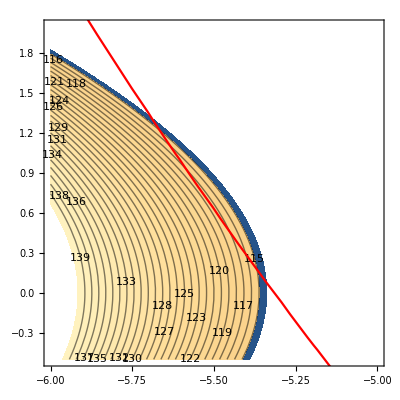

```mathematica
Show[ContourPlot[4 x^2-9 y^2,{x,-6,-5},{y,-0.5,2},PlotRange->{114,140},Contours->25,ContourLabels->All],ContourPlot[(x+2)^2-2y==11,{x,-8,-2},{y,-4,6},ContourStyle->Red]]
```

For F. The maxima is117.5, this picture suggests that no other contour will be tangent to the constraint curve therefore there will be no minimal output.